General MagneticTB Examples

The following examples show how to construct models for graphene, MoS2, magnetic Weyl points, nodal lines, and a C4 topological insulator. For each model, first specify the lattice, atomic positions, symmetry, and orbitals. Then calculate the Hamiltonian, assign its parameters, and plot the bands. Some examples also calculate a Chern number or export Wannier90 hopping data.

```mathematica
Needs["MagneticTB`"]
```

Graphene

Start with graphene, retaining one pz orbital on each carbon atom. The complete input below gives the two-band Hamiltonian with onsite, nearest-neighbor, and second-neighbor terms:

```mathematica
grapheneOperations = msgop[gray[191]];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 3},
  wyckoffposition -> {
    {{1/3, 2/3, 0}, {0, 0, 0}}
  },
  symminformation -> grapheneOperations,
  basisFunctions -> {{"pz"}},
  InitialBondShells -> 3,
  GenerateSymmetryGroup -> False
];
grapheneOnsite = symham[1];
grapheneNearest = symham[2];
grapheneNextNearest = symham[3];
grapheneHamiltonian =
  grapheneOnsite + grapheneNearest + grapheneNextNearest;
MatrixForm[
  FullSimplify[
    ExpToTrig[grapheneHamiltonian],
    Element[{kx, ky, kz}, Reals]
  ]
]
```

(e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]) | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]))

```mathematica
graphenePath = {
  {{{0, 0, 0}, {0, 1/2, 0}}, {"G", "M"}},
  {{{0, 1/2, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}}
};
```

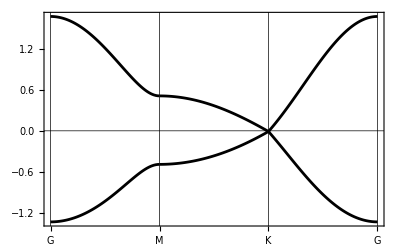

```mathematica
bandplot[
  graphenePath, 60, grapheneHamiltonian,
  {e1 -> 0.05, r1 -> 0.02, t1 -> 0.5}
]
```

Spinful graphene, interactive SOC bands, and Wannier90 export

To include spin-orbit coupling, replace pz by {pzup,pzdn} on each carbon atom. There are now four basis states. The gray group includes time reversal, and symham gives the spin-dependent terms allowed by this symmetry. We use this Hamiltonian below to plot bands and export Wannier90 data.

```mathematica
spinfulGrapheneOperations = msgop[gray[191]];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 3},
  wyckoffposition -> {
    {{1/3, 2/3, 0}, {0, 0, 0}}
  },
  symminformation -> spinfulGrapheneOperations,
  basisFunctions -> {{"pzup", "pzdn"}},
  InitialBondShells -> 3,
  GenerateSymmetryGroup -> False
];
spinfulGrapheneHamiltonian = Sum[symham[i], {i, 3}];
spinfulGraphenePath = {
  {{{0, 0, 0}, {0, 1/2, 0}}, {"G", "M"}},
  {{{0, 1/2, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}}
};
spinfulGrapheneParameters = {
  e1 -> 0, r1 -> 0.02, r2 -> 0, t1 -> 0.5
};
```

```mathematica
MatrixForm[spinfulGrapheneHamiltonian]
```

(e1+ⅇ^(-ⅈ kx) (-ⅈ r1+r2)+ⅇ^(-ⅈ ky) (-ⅈ r1+r2)+ⅇ^(ⅈ (kx+ky)) (-ⅈ r1+r2)+ⅇ^(ⅈ kx) (ⅈ r1+r2)+ⅇ^(ⅈ (-kx-ky)) (ⅈ r1+r2)+ⅇ^(ⅈ ky) (ⅈ r1+r2) | 0 | ⅇ^(ⅈ (-(2 kx)/3-ky/3)) t1+ⅇ^(ⅈ (kx/3-ky/3)) t1+ⅇ^(ⅈ (kx/3+(2 ky)/3)) t1 | 0
0 | e1+ⅇ^(ⅈ kx) (-ⅈ r1+r2)+ⅇ^(ⅈ (-kx-ky)) (-ⅈ r1+r2)+ⅇ^(ⅈ ky) (-ⅈ r1+r2)+ⅇ^(-ⅈ kx) (ⅈ r1+r2)+ⅇ^(-ⅈ ky) (ⅈ r1+r2)+ⅇ^(ⅈ (kx+ky)) (ⅈ r1+r2) | 0 | ⅇ^(ⅈ (-(2 kx)/3-ky/3)) t1+ⅇ^(ⅈ (kx/3-ky/3)) t1+ⅇ^(ⅈ (kx/3+(2 ky)/3)) t1
ⅇ^(ⅈ (-kx/3-(2 ky)/3)) t1+ⅇ^(ⅈ (-kx/3+ky/3)) t1+ⅇ^(ⅈ ((2 kx)/3+ky/3)) t1 | 0 | e1+ⅇ^(ⅈ kx) (-ⅈ r1+r2)+ⅇ^(ⅈ (-kx-ky)) (-ⅈ r1+r2)+ⅇ^(ⅈ ky) (-ⅈ r1+r2)+ⅇ^(-ⅈ kx) (ⅈ r1+r2)+ⅇ^(-ⅈ ky) (ⅈ r1+r2)+ⅇ^(ⅈ (kx+ky)) (ⅈ r1+r2) | 0
0 | ⅇ^(ⅈ (-kx/3-(2 ky)/3)) t1+ⅇ^(ⅈ (-kx/3+ky/3)) t1+ⅇ^(ⅈ ((2 kx)/3+ky/3)) t1 | 0 | e1+ⅇ^(-ⅈ kx) (-ⅈ r1+r2)+ⅇ^(-ⅈ ky) (-ⅈ r1+r2)+ⅇ^(ⅈ (kx+ky)) (-ⅈ r1+r2)+ⅇ^(ⅈ kx) (ⅈ r1+r2)+ⅇ^(ⅈ (-kx-ky)) (ⅈ r1+r2)+ⅇ^(ⅈ ky) (ⅈ r1+r2))

Run the following command to display the parameter sliders. Move them to see how the bands change:

```mathematica
bandManipulate[spinfulGraphenePath, 30, spinfulGrapheneHamiltonian]
```

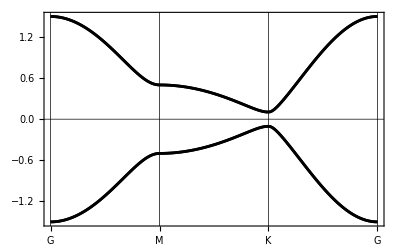

```mathematica
bandplot[
  spinfulGraphenePath,
  60,
  spinfulGrapheneHamiltonian,
  spinfulGrapheneParameters
]
```

After symham has obtained the hopping terms, use hop to write them to a Wannier90 HR file. The beginning of the file is shown below:

```mathematica
spinfulGrapheneHR = FileNameJoin[{
  $TemporaryDirectory,
  "spinful-graphene_hr.dat"
}];
hop[
  {1, 2, 3},
  spinfulGrapheneParameters,
  "hrExport" -> spinfulGrapheneHR
];
Take[Import[spinfulGrapheneHR, "Lines"], 12]
```

{Generated by MagneticTB,4,7,1 1 1 1 1 1 1,-1 -1 0 1 1 0.000000000000 0.020000000000,-1 -1 0 2 1 0.000000000000 0.000000000000,-1 -1 0 3 1 0.000000000000 0.000000000000,-1 -1 0 4 1 0.000000000000 0.000000000000,-1 -1 0 1 2 0.000000000000 0.000000000000,-1 -1 0 2 2 0.000000000000 -0.020000000000,-1 -1 0 3 2 0.000000000000 0.000000000000,-1 -1 0 4 2 0.000000000000 0.000000000000}

The header gives the number of Wannier orbitals and translation vectors. Each hopping entry then gives a translation vector, two orbital indices, and the real and imaginary parts of the matrix element.

Three-band MoS2 model

For monolayer MoS2, keep the three local orbitals dz2, dxy, and dx2-y2. The substitution after symham converts the parameters to the convention used in the MagneticTB 1.0 example. Assign moS2Parameters only after this conversion, so each value corresponds to the intended matrix element.

Reference: G.-B. Liu, W.-Y. Shan, Y. Yao, W. Yao, and D. Xiao, "Three-band tight-binding model for monolayers of group-VIB transition metal dichalcogenides," Physical Review B 88, 085433 (2013), https://doi.org/10.1103/PhysRevB.88.085433. The example below uses the three-band model and parameter values from the MagneticTB 1.0 example; the parameter conversion does not change its numerical Hamiltonian.

```mathematica
moS2Operations = msgop[gray[187]];
moS2BasisTransform = {{1, -1, 0}, {0, 1, 0}, {0, 0, 1}};
moS2Operations = MapAt[
  Function[operation,
    FullSimplify[
      moS2BasisTransform.operation.
        Inverse[moS2BasisTransform]
    ]
  ],
  moS2Operations,
  {All, 2}
];
init[
  lattice -> {
    {1, 0, 0},
    {1/2, Sqrt[3]/2, 0},
    {0, 0, 100}
  },
  lattpar -> {},
  wyckoffposition -> {
    {{0, 0, 0}, {0, 0, 0}}
  },
  symminformation -> moS2Operations,
  basisFunctions -> {{"dz2", "dxy", "dx2-y2"}},
  InitialBondShells -> 2,
  GenerateSymmetryGroup -> False
];
moS2Hamiltonian = (symham[1] + symham[2]) /. {
  e1 -> e2, e2 -> e1,
  t1 -> t6, t2 -> t5, t3 -> t4,
  t4 -> t3, t5 -> t2, t6 -> t1
};
```

```mathematica
moS2Path = {
  {{{0, 0, 0}, {2/3, 1/3, 0}}, {"G", "K"}},
  {{{2/3, 1/3, 0}, {1/2, 1/2, 0}}, {"K", "M"}},
  {{{1/2, 1/2, 0}, {0, 0, 0}}, {"M", "G"}}
};
moS2Parameters = {
  e1 -> 1.046, e2 -> 2.104,
  t1 -> -0.184, t2 -> 0.401, t3 -> 0.218,
  t4 -> 0.507, t5 -> 0.338, t6 -> 0.057
};
```

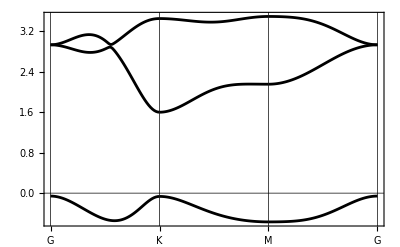

```mathematica
bandplot[moS2Path, 60, moS2Hamiltonian, moS2Parameters]
```

### Spinful MoS2 and two explicit basis orders

For the spinful onsite Hamiltonian, first place all spin-up orbitals before the spin-down orbitals. Specify the reduced symmetry in init before calculating the Hamiltonian:

```mathematica
moS2SpinAOperations = msgop[gray[187]];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 4},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 0}}},
  symminformation -> moS2SpinAOperations,
  basisFunctions -> {{"dz2up", "dxyup", "dx2-y2up", "dz2dn", "dxydn", "dx2-y2dn"}},
  InitialBondShells -> 1,
  GenerateSymmetryGroup -> False
];
moS2SpinARules = brokenSymmetryInitRules[{9, 11, 13}];
init @@ moS2SpinARules;
moS2SpinAHamiltonian = symham[1];
```

```mathematica
orbitalTable[]
```

Hamiltonian dimension = 6; representation mode = DirectProduct |  |  |  |  |  |  |  |  |  |  | 
H index | Site | Wyckoff orbit | Atom | Fractional position | Cartesian position | Local orbital | Input basis | Actual basis state | Spin structure | Spin state | Transport operation
1 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 1 | dz2up | {-x^2-y^2+2 z^2,0} | FactorizedSpinor | {1,0} | None
2 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 2 | dxyup | {2 x y,0} | FactorizedSpinor | {1,0} | None
3 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 3 | dx2-y2up | {x^2-y^2,0} | FactorizedSpinor | {1,0} | None
4 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 4 | dz2dn | {0,-x^2-y^2+2 z^2} | FactorizedSpinor | {0,1} | None
5 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 5 | dxydn | {0,2 x y} | FactorizedSpinor | {0,1} | None
6 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 6 | dx2-y2dn | {0,x^2-y^2} | FactorizedSpinor | {0,1} | None

```mathematica
MatrixForm[moS2SpinAHamiltonian]
```

(-e3 | 0 | 0 | 0 | 0 | 0
0 | -e2 | -ⅈ e1 | 0 | 0 | 0
0 | ⅈ e1 | -e2 | 0 | 0 | 0
0 | 0 | 0 | -e3 | 0 | 0
0 | 0 | 0 | 0 | -e2 | ⅈ e1
0 | 0 | 0 | 0 | -ⅈ e1 | -e2)

Alternatively, place the spin-up and spin-down states next to each other for each orbital. The order shown by orbitalTable is also the row and column order of the Hamiltonian:

```mathematica
moS2SpinBOperations = msgop[gray[187]];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 4},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 0}}},
  symminformation -> moS2SpinBOperations,
  basisFunctions -> {{"dz2up", "dz2dn", "dxyup", "dxydn", "dx2-y2up", "dx2-y2dn"}},
  InitialBondShells -> 1,
  GenerateSymmetryGroup -> False
];
moS2SpinBRules = brokenSymmetryInitRules[{9, 11, 13}];
init @@ moS2SpinBRules;
moS2SpinBHamiltonian = symham[1];
```

```mathematica
orbitalTable[]
```

Hamiltonian dimension = 6; representation mode = DirectProduct |  |  |  |  |  |  |  |  |  |  | 
H index | Site | Wyckoff orbit | Atom | Fractional position | Cartesian position | Local orbital | Input basis | Actual basis state | Spin structure | Spin state | Transport operation
1 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 1 | dz2up | {-x^2-y^2+2 z^2,0} | FactorizedSpinor | {1,0} | None
2 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 2 | dz2dn | {0,-x^2-y^2+2 z^2} | FactorizedSpinor | {0,1} | None
3 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 3 | dxyup | {2 x y,0} | FactorizedSpinor | {1,0} | None
4 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 4 | dxydn | {0,2 x y} | FactorizedSpinor | {0,1} | None
5 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 5 | dx2-y2up | {x^2-y^2,0} | FactorizedSpinor | {1,0} | None
6 | 1 | 1 | 1 | {0,0,0} | {0,0,0} | 6 | dx2-y2dn | {0,x^2-y^2} | FactorizedSpinor | {0,1} | None

```mathematica
MatrixForm[moS2SpinBHamiltonian]
```

(-e3 | 0 | 0 | 0 | 0 | 0
0 | -e3 | 0 | 0 | 0 | 0
0 | 0 | -e2 | 0 | -ⅈ e1 | 0
0 | 0 | 0 | -e2 | 0 | ⅈ e1
0 | 0 | ⅈ e1 | 0 | -e2 | 0
0 | 0 | 0 | -ⅈ e1 | 0 | -e2)

Magnetic C3 Weyl point and Chern diagnostic

For magnetic space group 143.3, the local spinor pair gives a four-band Hamiltonian. As in the MagneticTB 1.0 example, select the two-band block with row and column indices {1,4}. The replacement c3OriginalParameterCoordinates puts its parameters in the 1.0 convention before numerical values are assigned.

The parameters in this Weyl model and the following nodal-line and C4 models illustrate symmetry-allowed band structures. They are the values used in the MagneticTB 1.0 examples, not fitted parameters for a particular material.

```mathematica
c3Operations = msgop[bnsdict[{143, 3}]];
init[
  lattice -> {
    {Sqrt[3] a/2, -a/2, 0},
    {0, a, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 2},
  wyckoffposition -> {
    {{0, 0, 0}, {0, 0, 1}}
  },
  symminformation -> c3Operations,
  basisFunctions -> {{{x + I y, 0}, {0, x - I y}}},
  InitialBondShells -> 4,
  GenerateSymmetryGroup -> False
];
c3Full = Sum[symham[i], {i, {2, 3, 4}}];
c3OriginalParameterCoordinates = {
  r11 -> -r2, r15 -> -r10,
  r3 -> -r6, r7 -> -r14,
  s4 -> -s4,
  t4 -> t1, t8 -> t9, t11 -> -t7
};
c3Hamiltonian =
  c3Full[[{1, 4}, {1, 4}]] /.
    c3OriginalParameterCoordinates;
```

The full two-band c3Hamiltonian is used for the band plot and Chern-number calculation below. To see its matrix elements more clearly, first display it on Gamma-A by setting kx=ky=0:

```mathematica
c3GammaAxisHamiltonian = FullSimplify[
  c3Hamiltonian /. {kx -> 0, ky -> 0},
  Element[kz, Reals]
];
MatrixForm[c3GammaAxisHamiltonian]
```

(6 (s8+t9) | -2 ⅈ (3 r10-3 r14+3 ⅈ r2-3 ⅈ r6+t15-ⅈ t7) Sin[kz/2]
2 ⅈ (3 r10-3 r14-3 ⅈ r2+3 ⅈ r6+t15+ⅈ t7) Sin[kz/2] | 6 (s8+t9))

```mathematica
c3Path = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"G", "M"}},
  {{{1/2, 0, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}},
  {{{0, 0, 0}, {0, 0, 1/2}}, {"G", "A"}},
  {{{0, 0, 1/2}, {1/2, 0, 1/2}}, {"A", "L"}},
  {{{1/2, 0, 1/2}, {1/3, 1/3, 1/2}}, {"L", "H"}},
  {{{1/3, 1/3, 1/2}, {0, 0, 1/2}}, {"H", "A"}},
  {{{1/2, 0, 1/2}, {1/2, 0, 0}}, {"L", "M"}},
  {{{1/3, 1/3, 0}, {1/3, 1/3, 1/2}}, {"K", "H"}}
};
c3Parameters = {
  r10 -> -0.09, r14 -> 0.25, r2 -> 0, r6 -> 0.5,
  s4 -> -0.38, s8 -> 0, t1 -> 0,
  t15 -> 0.735, t7 -> 0.05, t9 -> 0.015
};
```

Use the following command to adjust the parameters and view the bands:

```mathematica
bandManipulate[c3Path, 20, c3Hamiltonian]
```

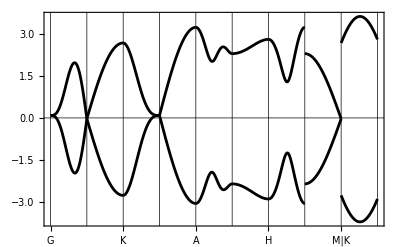

```mathematica
bandplot[c3Path, 200, c3Hamiltonian, c3Parameters]
```

Expand the Hamiltonian about Gamma through total order three, then pass it to pointChernNumber. The function calculates the occupied-band Berry flux through a cube surrounding the point. The occupied band must remain separated from the other band on the cube surface; the enclosed Chern number is given below.

```mathematica
c3Taylor = Expand@Normal@Chop@Series[
  c3Hamiltonian, {ky, 0, 3}, {kx, 0, 3}, {kz, 0, 3}
];
c3Taylor = FromCoefficientRules[
  Map[
    Select[#, Total[First[#]] <= 3 &] & ,
    CoefficientRules[c3Taylor, {kx, ky, kz}],
    {2}
  ],
  {kx, ky, kz}
];
c3Numeric[momentum_List] := N[
  c3Taylor /. c3Parameters /.
    Thread[{kx, ky, kz} -> momentum]
];
```

```mathematica
pointChernNumber[
  c3Numeric, 1, {0, 0, 0}, 2,
  "SurfaceSubdivisions" -> 8
]
```

3

Magnetic cubic nodal line

Next use magnetic space group 184.196 with the same local spinor basis. The operations numbered {2,7,13} in the MagneticTB 1.0 example generate this 24-operation group; init below receives the full group. Again select the {1,4} two-band block, and use nodalOriginalParameterCoordinates to put its parameters in the 1.0 convention.

```mathematica
nodalOperations = msgop[bnsdict[{184, 196}]];
init[
  lattice -> {
    {Sqrt[3] a/2, -a/2, 0},
    {0, a, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 2},
  wyckoffposition -> {
    {{0, 0, 0}, {0, 0, 1}}
  },
  symminformation -> nodalOperations,
  basisFunctions -> {{{x + I y, 0}, {0, x - I y}}},
  InitialBondShells -> 5,
  GenerateSymmetryGroup -> False
];
nodalFull = Sum[symham[i], {i, 5}];
nodalOriginalParameterCoordinates = {
  p5n1 -> p5n4, p5n8 -> p5n2,
  s1 -> s3, t1 -> t2,
  p5n6 -> -p5n7, r2 -> -r1
};
nodalHamiltonian =
  nodalFull[[{1, 4}, {1, 4}]] /.
    nodalOriginalParameterCoordinates;
```

```mathematica
MatrixForm[nodalHamiltonian]
```

(e2+ⅇ^(-ⅈ kz) p5n2+ⅇ^(ⅈ kz) p5n2+ⅇ^(-2 ⅈ kx) p5n4+ⅇ^(2 ⅈ kx) p5n4+ⅇ^(ⅈ (-2 kx-2 ky)) p5n4+ⅇ^(-2 ⅈ ky) p5n4+ⅇ^(2 ⅈ ky) p5n4+ⅇ^(ⅈ (2 kx+2 ky)) p5n4+ⅇ^(ⅈ (-kx-2 ky)) s3+ⅇ^(ⅈ (-2 kx-ky)) s3+ⅇ^(ⅈ (kx-ky)) s3+ⅇ^(ⅈ (-kx+ky)) s3+ⅇ^(ⅈ (2 kx+ky)) s3+ⅇ^(ⅈ (kx+2 ky)) s3+ⅇ^(-ⅈ kx) t2+ⅇ^(ⅈ kx) t2+ⅇ^(ⅈ (-kx-ky)) t2+ⅇ^(-ⅈ ky) t2+ⅇ^(ⅈ ky) t2+ⅇ^(ⅈ (kx+ky)) t2 | ⅇ^(ⅈ (-kx-2 ky-kz/2)) p5n7-ⅇ^(ⅈ (-2 kx-ky-kz/2)) p5n7-ⅇ^(ⅈ (kx-ky-kz/2)) p5n7+ⅇ^(ⅈ (-kx+ky-kz/2)) p5n7+ⅇ^(ⅈ (2 kx+ky-kz/2)) p5n7-ⅇ^(ⅈ (kx+2 ky-kz/2)) p5n7+ⅇ^(ⅈ (-kx-2 ky+kz/2)) p5n7-ⅇ^(ⅈ (-2 kx-ky+kz/2)) p5n7-ⅇ^(ⅈ (kx-ky+kz/2)) p5n7+ⅇ^(ⅈ (-kx+ky+kz/2)) p5n7+ⅇ^(ⅈ (2 kx+ky+kz/2)) p5n7-ⅇ^(ⅈ (kx+2 ky+kz/2)) p5n7+ⅈ ⅇ^(ⅈ (-kx-kz/2)) r1-ⅈ ⅇ^(ⅈ (kx-kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (-kx+kz/2)) r1-ⅈ ⅇ^(ⅈ (kx+kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (ky+kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky+kz/2)) r1
-ⅇ^(ⅈ (-kx-2 ky-kz/2)) p5n7+ⅇ^(ⅈ (-2 kx-ky-kz/2)) p5n7+ⅇ^(ⅈ (kx-ky-kz/2)) p5n7-ⅇ^(ⅈ (-kx+ky-kz/2)) p5n7-ⅇ^(ⅈ (2 kx+ky-kz/2)) p5n7+ⅇ^(ⅈ (kx+2 ky-kz/2)) p5n7-ⅇ^(ⅈ (-kx-2 ky+kz/2)) p5n7+ⅇ^(ⅈ (-2 kx-ky+kz/2)) p5n7+ⅇ^(ⅈ (kx-ky+kz/2)) p5n7-ⅇ^(ⅈ (-kx+ky+kz/2)) p5n7-ⅇ^(ⅈ (2 kx+ky+kz/2)) p5n7+ⅇ^(ⅈ (kx+2 ky+kz/2)) p5n7+ⅈ ⅇ^(ⅈ (-kx-kz/2)) r1-ⅈ ⅇ^(ⅈ (kx-kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (-kx+kz/2)) r1-ⅈ ⅇ^(ⅈ (kx+kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (ky+kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky+kz/2)) r1 | e2+ⅇ^(-ⅈ kz) p5n2+ⅇ^(ⅈ kz) p5n2+ⅇ^(-2 ⅈ kx) p5n4+ⅇ^(2 ⅈ kx) p5n4+ⅇ^(ⅈ (-2 kx-2 ky)) p5n4+ⅇ^(-2 ⅈ ky) p5n4+ⅇ^(2 ⅈ ky) p5n4+ⅇ^(ⅈ (2 kx+2 ky)) p5n4+ⅇ^(ⅈ (-kx-2 ky)) s3+ⅇ^(ⅈ (-2 kx-ky)) s3+ⅇ^(ⅈ (kx-ky)) s3+ⅇ^(ⅈ (-kx+ky)) s3+ⅇ^(ⅈ (2 kx+ky)) s3+ⅇ^(ⅈ (kx+2 ky)) s3+ⅇ^(-ⅈ kx) t2+ⅇ^(ⅈ kx) t2+ⅇ^(ⅈ (-kx-ky)) t2+ⅇ^(-ⅈ ky) t2+ⅇ^(ⅈ ky) t2+ⅇ^(ⅈ (kx+ky)) t2)

Run the last line to display the sliders and plot the bands:

```mathematica
nodalPath = {
  {{{0, 1/10, 1/4}, {0, 0, 1/4}}, {"Q", "P"}},
  {{{0, 0, 1/4}, {-1/10, 1/15, 1/4}}, {"P", "Q'"}}
};
bandManipulate[nodalPath, 100, nodalHamiltonian]
```

C4 topological-insulator model

This model has two inequivalent Wyckoff positions and two local orbitals. Keep the indicated neighbor hoppings and make the parameter substitutions shown below, as in the MagneticTB 1.0 example:

```mathematica
c4Operations = msgop[gray[75]];
init[
  lattice -> {
    {a, 0, 0},
    {0, a, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 1},
  wyckoffposition -> {
    {{0, 0, 1/4}, {0, 0, 0}},
    {{0, 0, 0}, {0, 0, 0}}
  },
  symminformation -> c4Operations,
  basisFunctions -> {{"px", "py"}, {"px", "py"}},
  InitialBondShells -> 7,
  GenerateSymmetryGroup -> False
];
c4Raw = Association@Table[
  shell -> symham[shell],
  {shell, {2, 3, 4, 5, 7}}
];
```

```mathematica
c4Hamiltonian = FullSimplify[
  (c4Raw[2] /. {t1 -> 0, t2 -> t1p}) +
  (c4Raw[3] /. {r1 -> 0, r2 -> tzp}) +
  (c4Raw[4] /. {
    s10 -> 0, s7 -> 0, s9 -> 0, s2 -> 0,
    s4 -> 0, s1 -> 0, s6 -> 0, s5 -> 0,
    s8 -> t1a, s3 -> t1b
  }) +
  ((c4Raw[5] /. {p5n2 -> 0, p5n3 -> 0, p5n1 -> p5n4}) /.
    p5n4 -> t2p) +
  ((c4Raw[7] /. {
    p7n7 -> p7n5, p7n1 -> 0, p7n4 -> 0,
    p7n2 -> 0, p7n3 -> 0, p7n14 -> p7n12,
    p7n11 -> 0, p7n8 -> 0, p7n10 -> 0,
    p7n9 -> 0, p7n6 -> -p7n5, p7n13 -> p7n12
  }) /. {p7n5 -> t2a/2, p7n12 -> t2b/2})
];
MatrixForm[symhamII[c4Hamiltonian]]
```

(ⅇ^(-ⅈ ky) t1b+ⅇ^(ⅈ ky) t1b+1/2 ⅇ^(-ⅈ kx-ⅈ kz) t2a+1/2 ⅇ^(ⅈ kx-ⅈ kz) t2a+1/2 ⅇ^(-ⅈ kx+ⅈ kz) t2a+1/2 ⅇ^(ⅈ kx+ⅈ kz) t2a | -1/2 ⅇ^(-ⅈ kx-ⅈ kz) t2a-1/2 ⅇ^(ⅈ kx-ⅈ kz) t2a-1/2 ⅇ^(-ⅈ ky-ⅈ kz) t2a-1/2 ⅇ^(ⅈ ky-ⅈ kz) t2a+1/2 ⅇ^(-ⅈ kx+ⅈ kz) t2a+1/2 ⅇ^(ⅈ kx+ⅈ kz) t2a+1/2 ⅇ^(-ⅈ ky+ⅈ kz) t2a+1/2 ⅇ^(ⅈ ky+ⅈ kz) t2a | -t1p+ⅇ^(-ⅈ kx) t2p+ⅇ^(ⅈ kx) t2p+ⅇ^(-ⅈ ky) t2p+ⅇ^(ⅈ ky) t2p-ⅇ^(ⅈ kz) tzp | 0
1/2 ⅇ^(-ⅈ kx-ⅈ kz) t2a+1/2 ⅇ^(ⅈ kx-ⅈ kz) t2a+1/2 ⅇ^(-ⅈ ky-ⅈ kz) t2a+1/2 ⅇ^(ⅈ ky-ⅈ kz) t2a-1/2 ⅇ^(-ⅈ kx+ⅈ kz) t2a-1/2 ⅇ^(ⅈ kx+ⅈ kz) t2a-1/2 ⅇ^(-ⅈ ky+ⅈ kz) t2a-1/2 ⅇ^(ⅈ ky+ⅈ kz) t2a | ⅇ^(-ⅈ kx) t1b+ⅇ^(ⅈ kx) t1b+1/2 ⅇ^(-ⅈ ky-ⅈ kz) t2a+1/2 ⅇ^(ⅈ ky-ⅈ kz) t2a+1/2 ⅇ^(-ⅈ ky+ⅈ kz) t2a+1/2 ⅇ^(ⅈ ky+ⅈ kz) t2a | 0 | -t1p+ⅇ^(-ⅈ kx) t2p+ⅇ^(ⅈ kx) t2p+ⅇ^(-ⅈ ky) t2p+ⅇ^(ⅈ ky) t2p-ⅇ^(ⅈ kz) tzp
-t1p+ⅇ^(-ⅈ kx) t2p+ⅇ^(ⅈ kx) t2p+ⅇ^(-ⅈ ky) t2p+ⅇ^(ⅈ ky) t2p-ⅇ^(-ⅈ kz) tzp | 0 | ⅇ^(-ⅈ ky) t1a+ⅇ^(ⅈ ky) t1a+1/2 ⅇ^(-ⅈ kx-ⅈ kz) t2b+1/2 ⅇ^(ⅈ kx-ⅈ kz) t2b+1/2 ⅇ^(-ⅈ kx+ⅈ kz) t2b+1/2 ⅇ^(ⅈ kx+ⅈ kz) t2b | 1/2 ⅇ^(-ⅈ kx-ⅈ kz) t2b+1/2 ⅇ^(ⅈ kx-ⅈ kz) t2b-1/2 ⅇ^(-ⅈ ky-ⅈ kz) t2b-1/2 ⅇ^(ⅈ ky-ⅈ kz) t2b+1/2 ⅇ^(-ⅈ kx+ⅈ kz) t2b+1/2 ⅇ^(ⅈ kx+ⅈ kz) t2b-1/2 ⅇ^(-ⅈ ky+ⅈ kz) t2b-1/2 ⅇ^(ⅈ ky+ⅈ kz) t2b
0 | -t1p+ⅇ^(-ⅈ kx) t2p+ⅇ^(ⅈ kx) t2p+ⅇ^(-ⅈ ky) t2p+ⅇ^(ⅈ ky) t2p-ⅇ^(-ⅈ kz) tzp | 1/2 ⅇ^(-ⅈ kx-ⅈ kz) t2b+1/2 ⅇ^(ⅈ kx-ⅈ kz) t2b-1/2 ⅇ^(-ⅈ ky-ⅈ kz) t2b-1/2 ⅇ^(ⅈ ky-ⅈ kz) t2b+1/2 ⅇ^(-ⅈ kx+ⅈ kz) t2b+1/2 ⅇ^(ⅈ kx+ⅈ kz) t2b-1/2 ⅇ^(-ⅈ ky+ⅈ kz) t2b-1/2 ⅇ^(ⅈ ky+ⅈ kz) t2b | ⅇ^(-ⅈ kx) t1a+ⅇ^(ⅈ kx) t1a+1/2 ⅇ^(-ⅈ ky-ⅈ kz) t2b+1/2 ⅇ^(ⅈ ky-ⅈ kz) t2b+1/2 ⅇ^(-ⅈ ky+ⅈ kz) t2b+1/2 ⅇ^(ⅈ ky+ⅈ kz) t2b)

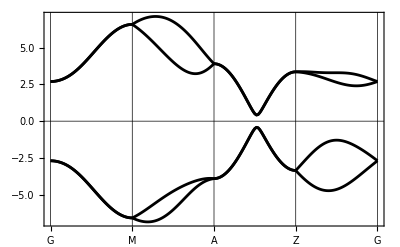

```mathematica
c4Path = {
  {{{0, 0, 0}, {1/2, 1/2, 0}}, {"G", "M"}},
  {{{1/2, 1/2, 0}, {1/2, 1/2, 1/2}}, {"M", "A"}},
  {{{1/2, 1/2, 1/2}, {0, 0, 1/2}}, {"A", "Z"}},
  {{{0, 0, 1/2}, {0, 0, 0}}, {"Z", "G"}}
};
bandplot[c4Path, 50, c4Hamiltonian, {
  t1a -> 1, t1b -> -1, t2a -> 0.5, t2b -> -0.5,
  t1p -> 2.5, t2p -> 0.5, tzp -> 2
}]
```

Wyckoff, layer-group, and rod-group databases

The symmetry databases can also be used on their own. showMSGWyckoff lists the representative positions and allowed moments of a magnetic space group. mlgop and mrgop give the operations of magnetic layer groups and magnetic rod groups, respectively.

```mathematica
showMSGWyckoff[gray[193]]
```

Multiplicity | Wyckoff Letter | Atomic Positions & Magnetization directions
2 | a | {0,0,1/4} | {0,0,0}
{0,0,3/4} | {0,0,0}
2 | b | {0,0,0} | {0,0,0}
{0,0,1/2} | {0,0,0}
4 | c | {1/3,2/3,1/4} | {0,0,0}
{2/3,1/3,3/4} | {0,0,0}
{2/3,1/3,1/4} | {0,0,0}
{1/3,2/3,3/4} | {0,0,0}
4 | d | {1/3,2/3,0} | {0,0,0}
{2/3,1/3,1/2} | {0,0,0}
{2/3,1/3,0} | {0,0,0}
{1/3,2/3,1/2} | {0,0,0}
4 | e | {0,0,z} | {0,0,0}
{0,0,1/2+z} | {0,0,0}
{0,0,1/2-z} | {0,0,0}
{0,0,-z} | {0,0,0}
6 | f | {1/2,0,0} | {0,0,0}
{1/2,1/2,1/2} | {0,0,0}
{0,1/2,0} | {0,0,0}
{1/2,0,1/2} | {0,0,0}
{1/2,1/2,0} | {0,0,0}
{0,1/2,1/2} | {0,0,0}
6 | g | {x,0,1/4} | {0,0,0}
{x,x,3/4} | {0,0,0}
{0,x,1/4} | {0,0,0}
{-x,0,3/4} | {0,0,0}
{-x,-x,1/4} | {0,0,0}
{0,-x,3/4} | {0,0,0}
8 | h | {1/3,2/3,z} | {0,0,0}
{2/3,1/3,1/2+z} | {0,0,0}
{2/3,1/3,1/2-z} | {0,0,0}
{1/3,2/3,-z} | {0,0,0}
{2/3,1/3,-z} | {0,0,0}
{1/3,2/3,1/2-z} | {0,0,0}
{1/3,2/3,1/2+z} | {0,0,0}
{2/3,1/3,z} | {0,0,0}
12 | i | {x,2 x,0} | {0,0,0}
{-x,x,1/2} | {0,0,0}
{-2 x,-x,0} | {0,0,0}
{-x,-2 x,1/2} | {0,0,0}
{x,-x,0} | {0,0,0}
{2 x,x,1/2} | {0,0,0}
{-x,-2 x,0} | {0,0,0}
{x,-x,1/2} | {0,0,0}
{2 x,x,0} | {0,0,0}
{x,2 x,1/2} | {0,0,0}
{-x,x,0} | {0,0,0}
{-2 x,-x,1/2} | {0,0,0}
12 | j | {x,y,1/4} | {0,0,0}
{x-y,x,3/4} | {0,0,0}
{-y,x-y,1/4} | {0,0,0}
{-x,-y,3/4} | {0,0,0}
{-x+y,-x,1/4} | {0,0,0}
{y,-x+y,3/4} | {0,0,0}
{x-y,-y,1/4} | {0,0,0}
{y,x,1/4} | {0,0,0}
{-x,-x+y,1/4} | {0,0,0}
{x,x-y,3/4} | {0,0,0}
{-x+y,y,3/4} | {0,0,0}
{-y,-x,3/4} | {0,0,0}
12 | k | {x,0,z} | {0,0,0}
{x,x,1/2+z} | {0,0,0}
{0,x,z} | {0,0,0}
{-x,0,1/2+z} | {0,0,0}
{-x,-x,z} | {0,0,0}
{0,-x,1/2+z} | {0,0,0}
{x,0,1/2-z} | {0,0,0}
{0,x,1/2-z} | {0,0,0}
{-x,-x,1/2-z} | {0,0,0}
{x,x,-z} | {0,0,0}
{-x,0,-z} | {0,0,0}
{0,-x,-z} | {0,0,0}
24 | l | {x,y,z} | {0,0,0}
{x-y,x,1/2+z} | {0,0,0}
{-y,x-y,z} | {0,0,0}
{-x,-y,1/2+z} | {0,0,0}
{-x+y,-x,z} | {0,0,0}
{y,-x+y,1/2+z} | {0,0,0}
{x-y,-y,1/2-z} | {0,0,0}
{y,x,1/2-z} | {0,0,0}
{-x,-x+y,1/2-z} | {0,0,0}
{x,x-y,-z} | {0,0,0}
{-x+y,y,-z} | {0,0,0}
{-y,-x,-z} | {0,0,0}
{-x,-y,-z} | {0,0,0}
{-x+y,-x,1/2-z} | {0,0,0}
{y,-x+y,-z} | {0,0,0}
{x,y,1/2-z} | {0,0,0}
{x-y,x,-z} | {0,0,0}
{-y,x-y,1/2-z} | {0,0,0}
{-x+y,y,1/2+z} | {0,0,0}
{-y,-x,1/2+z} | {0,0,0}
{x,x-y,1/2+z} | {0,0,0}
{-x,-x+y,z} | {0,0,0}
{x-y,-y,z} | {0,0,0}
{y,x,z} | {0,0,0}

```mathematica
showMSGWyckoff[bnsdict[{187, 211}]]
```

Multiplicity | Wyckoff Letter | Atomic Positions & Magnetization directions
1 | a | {0,0,0} | {0,0,0}
1 | b | {0,0,1/2} | {0,0,0}
1 | c | {1/3,2/3,0} | {0,0,0}
1 | d | {1/3,2/3,1/2} | {0,0,0}
1 | e | {2/3,1/3,0} | {0,0,0}
1 | f | {2/3,1/3,1/2} | {0,0,0}
2 | g | {0,0,z} | {0,0,mz}
{0,0,-z} | {0,0,-mz}
2 | h | {1/3,2/3,z} | {0,0,mz}
{1/3,2/3,-z} | {0,0,-mz}
2 | i | {2/3,1/3,z} | {0,0,mz}
{2/3,1/3,-z} | {0,0,-mz}
3 | j | {x,-x,0} | {mx,-mx,0}
{x,2 x,0} | {mx,2 mx,0}
{-2 x,-x,0} | {-2 mx,-mx,0}
3 | k | {x,-x,1/2} | {mx,-mx,0}
{x,2 x,1/2} | {mx,2 mx,0}
{-2 x,-x,1/2} | {-2 mx,-mx,0}
6 | l | {x,y,0} | {mx,my,0}
{-y,x-y,0} | {-my,mx-my,0}
{-x+y,-x,0} | {-mx+my,-mx,0}
{x,x-y,0} | {mx,mx-my,0}
{-x+y,y,0} | {-mx+my,my,0}
{-y,-x,0} | {-my,-mx,0}
6 | m | {x,y,1/2} | {mx,my,0}
{-y,x-y,1/2} | {-my,mx-my,0}
{-x+y,-x,1/2} | {-mx+my,-mx,0}
{x,x-y,1/2} | {mx,mx-my,0}
{-x+y,y,1/2} | {-mx+my,my,0}
{-y,-x,1/2} | {-my,-mx,0}
6 | n | {x,-x,z} | {mx,-mx,mz}
{x,2 x,z} | {mx,2 mx,mz}
{-2 x,-x,z} | {-2 mx,-mx,mz}
{x,2 x,-z} | {mx,2 mx,-mz}
{-2 x,-x,-z} | {-2 mx,-mx,-mz}
{x,-x,-z} | {mx,-mx,-mz}
12 | o | {x,y,z} | {mx,my,mz}
{-y,x-y,z} | {-my,mx-my,mz}
{-x+y,-x,z} | {-mx+my,-mx,mz}
{x,x-y,-z} | {mx,mx-my,-mz}
{-x+y,y,-z} | {-mx+my,my,-mz}
{-y,-x,-z} | {-my,-mx,-mz}
{-x+y,-x,-z} | {-mx+my,-mx,-mz}
{x,y,-z} | {mx,my,-mz}
{-y,x-y,-z} | {-my,mx-my,-mz}
{-x+y,y,z} | {-mx+my,my,mz}
{-y,-x,z} | {-my,-mx,mz}
{x,x-y,z} | {mx,mx-my,mz}

```mathematica
Take[mlgop[graylayer[25]], 4]
```

{{E,{{1,0,0},{0,1,0},{0,0,1}},{0,0,0},F},{C2z,{{-1,0,0},{0,-1,0},{0,0,1}},{0,0,0},F},{σx,{{-1,0,0},{0,1,0},{0,0,1}},{1/2,1/2,0},F},{σy,{{1,0,0},{0,-1,0},{0,0,1}},{1/2,1/2,0},F}}

```mathematica
Take[mlgop[{25, 3, 145}], 4]
```

{{E,{{1,0,0},{0,1,0},{0,0,1}},{0,0,0},F},{C2z,{{-1,0,0},{0,-1,0},{0,0,1}},{0,0,0},F},{σx,{{-1,0,0},{0,1,0},{0,0,1}},{1/2,1/2,0},T},{σy,{{1,0,0},{0,-1,0},{0,0,1}},{1/2,1/2,0},T}}

```mathematica
Take[mrgop[grayrod[25]], 4]
```

{{E,{{1,0,0},{0,1,0},{0,0,1}},{0,0,0},F},{C2z,{{-1,0,0},{0,-1,0},{0,0,1}},{0,0,0},F},{C4z+,{{0,-1,0},{1,0,0},{0,0,1}},{0,0,1/2},F},{C4z-,{{0,1,0},{-1,0,0},{0,0,1}},{0,0,1/2},F}}

```mathematica
Take[mrgop[{25, 3, 130}], 4]
```

{{E,{{1,0,0},{0,1,0},{0,0,1}},{0,0,0},F},{C4z+,{{0,-1,0},{1,0,0},{0,0,1}},{0,0,1/2},T},{C2z,{{-1,0,0},{0,-1,0},{0,0,1}},{0,0,0},F},{C4z-,{{0,1,0},{-1,0,0},{0,0,1}},{0,0,1/2},T}}

Changing the symmetry in version 2.0

To lower the symmetry, change the model inputs and run init again before calculating a new Hamiltonian. brokenSymmetryInitRules gives the retained subgroup and the resulting Wyckoff positions. Inspect these rules and pass them to init@@rules. The symmetry is set by init, not by a symmetryset option in symham.

MagneticTB help home

MagneticTB

History